```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction

```mathematica
Get["MergerTransport/Merger2DProton.m"]
```

## 0 spectrum

### algorithm to sort files according to last binnumber

```mathematica
FileSorter[Directory_]:=Module[
{filenames=FileNames["TransferResult*",Directory],splitted,orderedlist},
splitted=StringSplit[filenames,"-"];
orderedlist=Ordering[ToExpression[StringTake[splitted[[All,-1]],{1,-5}]]];
filenames[[orderedlist]]
]
```

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_G_da0_a-1050_1-49.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_G_da0_a-1050_50-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_G_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_G_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_G_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_G_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_G_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_G_da0_a-1050_179-264.txt}

```mathematica
RefSpectrum=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

### show single core timing

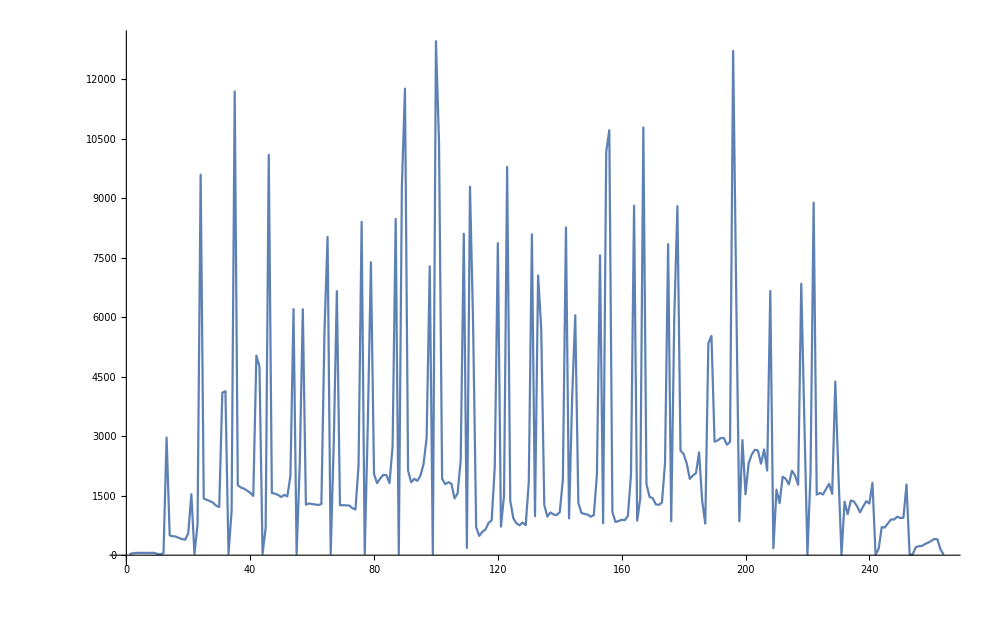

```mathematica
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000]
```

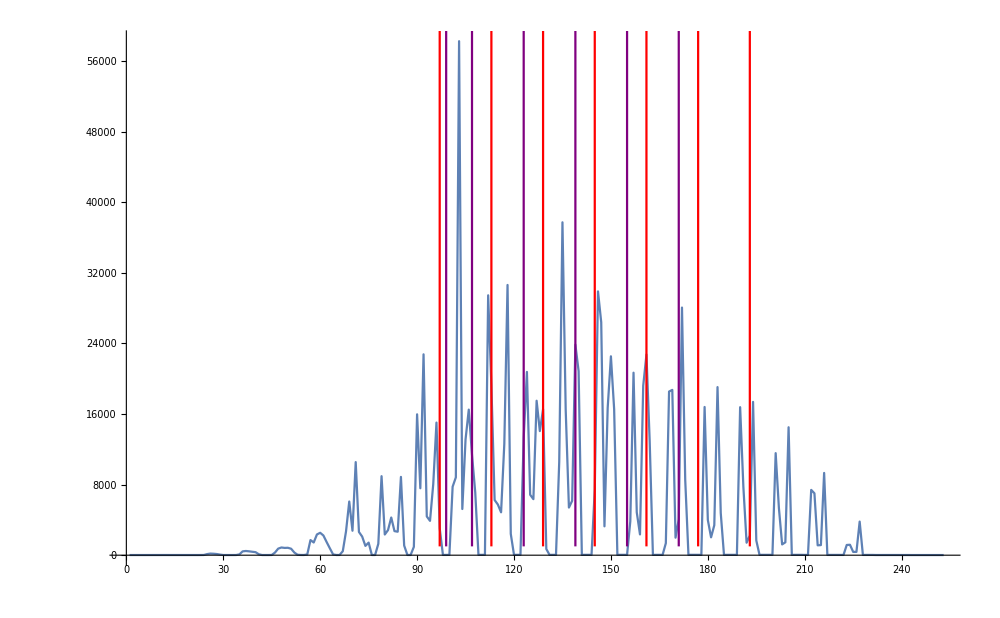

```mathematica
Show[
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000],
ParametricPlot[{{97,1000*d},{113,1000*d},{129,1000*d},{145,1000*d},{161,1000*d},{177,1000*d},{193,1000*d}},{d,1,253},PlotStyle->Red],
ParametricPlot[{{99,1000*d},{107,1000*d},{123,1000*d},{139,1000*d},{155,1000*d},{171,1000*d}},{d,1,253},PlotStyle->Purple]
]
```

## get Bin data

```mathematica
xStart=0.025;
xEnd=0.055;
yStart=-0.02;
yEnd=0.03;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
xyBins[[1]]
```

{{0.025,0.02625},{-0.02,-0.015909}}

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto={{-0.06999999999999999,-0.06499999999999999,-0.05999999999999999,-0.05499999999999999,-0.04999999999999999,-0.04499999999999999,-0.039999999999999994,-0.03499999999999999,-0.029999999999999992,-0.024999999999999994,-0.01999999999999999,-0.014999999999999993,-0.009999999999999995,-0.0049999999999999906,1.3877787807814457*^-17,0.0050000000000000044,0.010000000000000009,0.015000000000000013,0.020000000000000004,0.02500000000000001,0.030000000000000013,0.035,0.04000000000000001,0.045},{-1.0540019999999999,-1.049002,-1.0440019999999999,-1.039002,-1.0340019999999999,-1.029002,-1.0240019999999999,-1.019002,-1.0140019999999998,-1.009002,-1.0040019999999998,-0.9990019999999998,-0.9940019999999998,-0.9890019999999999,-0.9840019999999998,-0.9790019999999999,-0.9740019999999999,-0.9690019999999999,-0.9640019999999999,-0.9590019999999999,-0.9540019999999999,-0.9490019999999999,-0.9440019999999999},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=0.999002
```

0.999002

```mathematica
xyBins[[1,1]]
```

{0.025,0.02625}

```mathematica
Clear[BinCenters]
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(xyBins[[i,1,1]]+xyBins[[i,1,2]])/2,(xyBins[[i,2,1]]+xyBins[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

### Get XY Bins with Ybins halfed

```mathematica
XYBinBoundariesYHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1,1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

```mathematica
Length[XYBinBoundariesYHalf]
```

253

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
XYBinCentersYHalf[[1]]
```

{0.025625,-0.0179545}

## check spectrum

```mathematica
Transfer3DPlot=ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

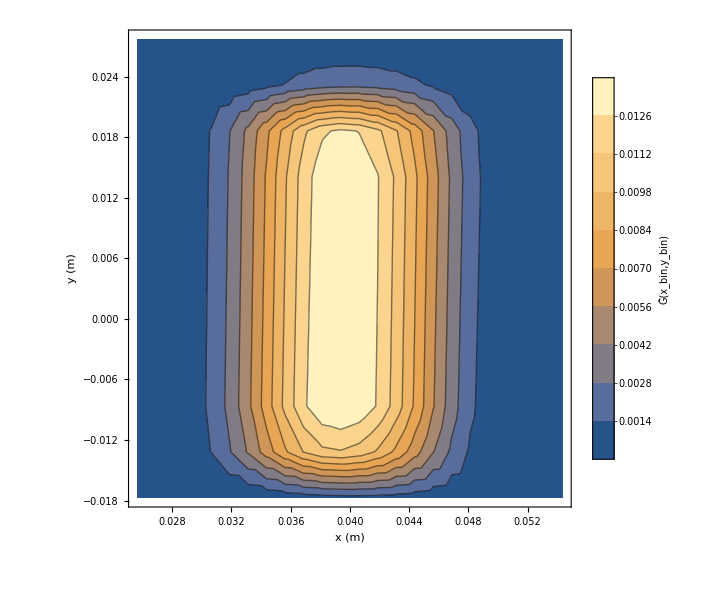

```mathematica
TransferContourPlot=ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/Transfer3D.png",Transfer3DPlot,ImageResolution->450];
Export["~/Dropbox/PhD/PhDLatex/Figures/TransferContour.png",TransferContourPlot,ImageResolution->450];*)
```

# dalpha, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1050/"];
```

```mathematica
dAlphaSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dAlpha_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1050_179-264.txt}

```mathematica
dAlphaSpectruma0=Flatten[Table[Import[dAlphaSubFileNamesa0[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa0]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1040/"];
```

```mathematica
dAlphaSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_179-264.txt}

```mathematica
dAlphaSpectruma1040=Flatten[Table[Import[dAlphaSubFileNamesa1040[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1040]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1045/"];
```

```mathematica
dAlphaSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1045_179-264.txt}

```mathematica
dAlphaSpectruma1045=Flatten[Table[Import[dAlphaSubFileNamesa1045[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1045]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1055/"];
```

```mathematica
dAlphaSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dAlpha_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1055_179-264.txt}

```mathematica
dAlphaSpectruma1055=Flatten[Table[Import[dAlphaSubFileNamesa1055[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1055]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1060/"];
```

```mathematica
dAlphaSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_1-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_155-178.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectruma1060=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,«11»,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,«214»},{«1»},{«1»}} cannot be transposed.

ListPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[{{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375},{-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225},{0.,4.47406×10^-7,6.02719×10^-7,5.91948×10^-7,5.81444×10^-7,5.712×10^-7,5.61209×10^-7,5.51466×10^-7,5.41964×10^-7,5.32696×10^-7,4.7537×10^-8,0.,0.0000879933,0.000119263,0.000117142,0.000115073,0.000113055,0.000111086,0.000109166,0.000107293,0.000105425,0.0000104972,0.,0.000701717,0.00095284,0.000936043,0.000919655,0.000903665,0.000888064,0.000872842,0.00085799,0.000839146,0.0000834918,3.58331×10^-6,0.00239424,0.00325984,0.00320332,0.00314813,0.00309426,0.00304166,0.00299032,0.0029402,0.00284964,0.00032744,0.000037153,0.00559786,0.00767212,0.00754258,0.00741597,0.00729226,0.00717136,0.00705324,0.00693783,0.00664814,0.000848275,0.000165107,0.0105381,0.0145968,0.0143608,0.0141297,0.0139035,0.0136821,0.0134654,0.0132533,0.0125425,0.00178013,0.000466431,0.0171216,0.0240332,0.0236796,0.0233293,0.0229846,0.0226455,0.0223122,0.0219845,0.0205554,0.00321431,0.000969803,0.0246907,0.03514,0.0347259,0.0342924,0.0338624,0.0334366,0.0330125,0.0325972,0.0301497,0.00514793,0.0015916,0.0322655,0.0464233,0.046046,0.045591,0.0451375,0.044685,0.0442348,0.0437858,0.0401527,0.00734276,0.00219509,0.038772,0.0562707,0.0560337,0.0556376,0.0552379,0.0548354,0.0544303,0.0540217,0.0492612,0.00942975,0.00266398,0.0428304,0.0626246,0.0626217,0.0623812,0.0621334,0.0618776,0.0616151,0.0613417,0.0557336,0.011034,0.00295508,0.0436891,0.0643134,0.0645129,0.0644494,0.0643665,0.0642769,0.0641834,0.0640785,0.0580297,0.0118594,0.00307598,0.0419072,0.0621049,0.0624825,0.0625327,0.0625775,0.0626192,0.0626546,0.062682,0.0565036,0.0119391,0.0030282,0.037831,0.0564824,0.0570017,0.0571843,0.0573608,0.0575318,0.0576844,0.0578408,0.0519172,0.0113515,0.00278317,0.0317702,0.0478251,0.0484799,0.0487967,0.0491074,0.0494123,0.0497108,0.0499994,0.0446937,0.010076,0.00232578,0.0244109,0.0370385,0.037772,0.0381898,0.0386031,0.0390119,0.0394162,0.0398116,0.0354807,0.00834065,0.00171498,0.0167973}}],PlotRange→All]

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,-0.05,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
dBRxBSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]]}]];
```

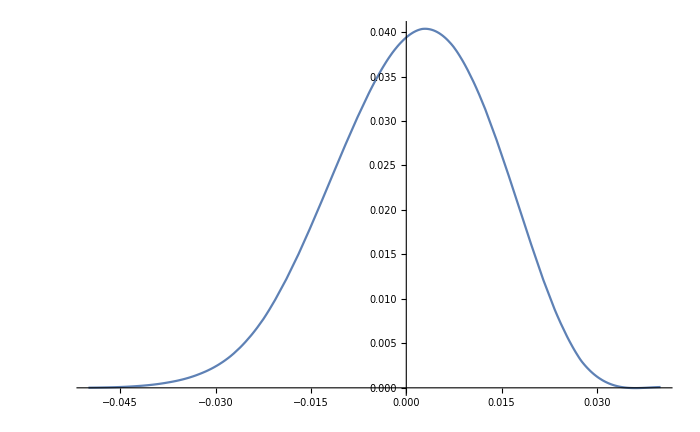

```mathematica
Plot[RefSpectrumInter[x,0.],{x,-0.05,0.04},PlotRange->All]
```

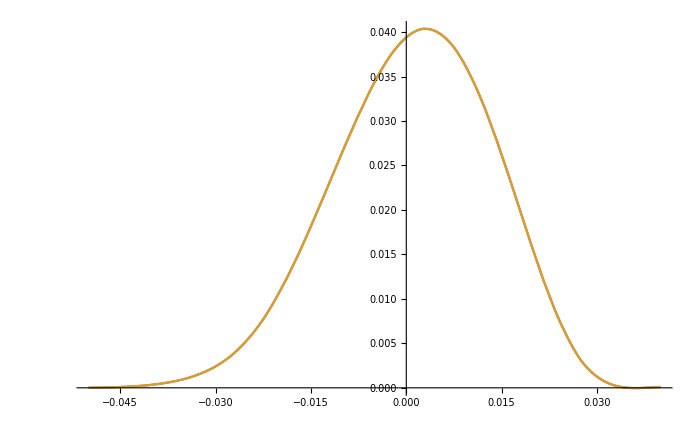

```mathematica
Plot[{RefSpectrumInter[x,0.],dBRxBSpectrumb0Inter[x,0.]},{x,-0.05,0.04},PlotRange->All]
```

```mathematica
dBRxBSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]]}]];
dBRxBSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm75[[All,2]]/Total[dBRxBSpectrumbm75[[All,2]]]}]];
dBRxBSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb15[[All,2]]/Total[dBRxBSpectrumb15[[All,2]]]}]];
dBRxBSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}]];
```

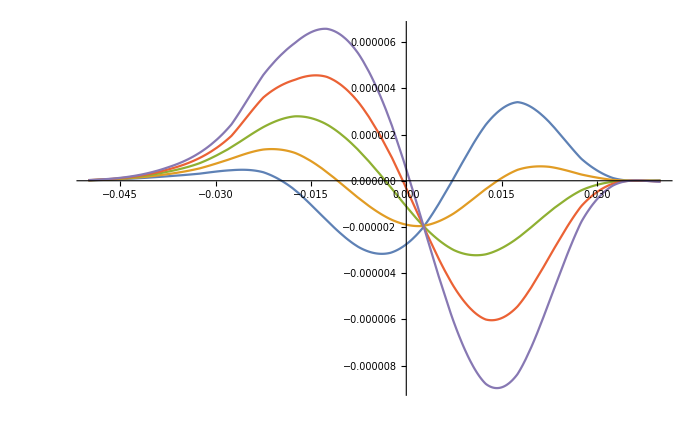

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBRxBSpectrumbm15Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumbm75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb0Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb15Inter[x,0.]
}
,{x,-0.05,0.04},PlotRange->All]
```

```mathematica
ListPlot[Total[(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-#)^2]&/@BRxBDataList]
```

ListPlot::lpn: BRxBDataList is not a list of numbers or pairs of numbers.

ListPlot[BRxBDataList]

```mathematica
dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.36863×10^-10,4.07996×10^-10,3.19292×10^-11,1.42553×10^-13,0.,0.,0.,0.,0.,0.,2.59993×10^-9,1.4643×10^-7,3.11107×10^-7,2.31112×10^-7,1.36065×10^-7,4.76193×10^-8,1.2291×10^-9,0.,0.,0.,0.,2.03998×10^-7,3.11947×10^-6,6.84058×10^-6,6.62686×10^-6,4.83431×10^-6,1.93743×10^-6,1.46401×10^-7,0.,0.,0.,7.05888×10^-10,3.16048×10^-6,0.0000234196,0.0000493116,0.0000531614,0.0000408369,0.0000188314,2.86494×10^-6,9.03721×10^-9,0.,0.,3.23234×10^-7,0.0000177044,0.000100397,0.000205907,0.000234623,0.000186966,0.0000927304,0.0000185237,5.51569×10^-7,0.,0.,9.71469×10^-7,0.0000595062,0.000309378,0.000628561,0.000736105,0.000600097,0.000310256,0.0000712827,3.0292×10^-6,0.,0.,2.74528×10^-6,0.000152579,0.000774239,0.00159952,0.0018878,0.00156135,0.000823198,0.000199853,9.54737×10^-6,0.,0.,3.88467×10^-6,0.000313669,0.00168782,0.00369996,0.00433486,0.00363987,0.00190851,0.000449662,0.0000222802,0.,0.,0.,0.000531094,0.00323004,0.00773746,0.00898466,0.00770991,0.00398244,0.000844609,0.0000358352,0.,0.,0.,0.000740222,0.00535976,0.0139127,0.0161335,0.0141924,0.0072312,0.00135022,0.0000226273,0.,0.,0.,0.000863278,0.00775098,0.0214202,0.0249538,0.0223604,0.0112936,0.00185325,7.06033×10^-7,0.,0.,0.,0.000809817,0.00986941,0.0288684,0.0337018,0.0306964,0.0153352,0.00211014,0.,0.,0.,0.,0.00054451,0.0110646,0.0345881,0.0402363,0.0373612,0.0183953,0.00197547,0.,0.,0.,0.,0.000206637,0.0108394,0.0369185,0.0424076,0.0403525,0.0194847,0.00143803,0.,0.,0.,0.,0.0000203655,0.00914436,0.0348098,0.0391745,0.0382876,0.0180841,0.000732696,0.,0.,0.,0.,0.,0.00645827,0.0283774,0.0311792,0.0311918,0.014377,0.000241551,0.,0.,0.,0.,0.,0.00375251,0.019043,0.0204596,0.0208311,0.00937791,0.000013516,0.,0.,0.,0.,0.,0.00163446,0.00951662,0.0100221,0.0102987,0.00457549,0.,0.,0.,0.,0.,0.,0.000440399,0.00285973,0.00296835,0.00305719,0.00136139,0.,0.,0.,0.,0.,0.,0.0000450576,0.000308296,0.000317597,0.000327138,0.000146399,0.,0.,0.,0.,0.,0.,4.85721×10^-8,3.66074×10^-7,3.75038×10^-7,3.84282×10^-7,6.12352×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## manual chi^2 investigation

```mathematica
10
```

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]],dAlphaSpectruma1045[[All,2]]/Total[dAlphaSpectruma1045[[All,2]]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]],dAlphaSpectruma1055[[All,2]]/Total[dAlphaSpectruma1055[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055}
```

{-0.104,-0.1045,-0.105,-0.1055}

```mathematica
dAlphaSpectruma1040[[All,2]]//Length
```

362

```mathematica
dAlphaSpectruma1055[[All,2]]//Length
```

264

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

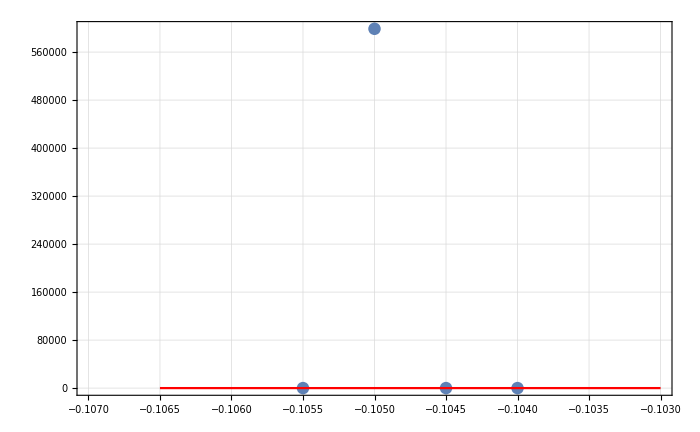
{{{5.34711×10^-10,2.3768×10^-10,0.000598782,9.7509×10^-12},{2.58071×10^-11,1.72935×10^-11,2.7387×10^-8,2.83817×10^-12}},a0 =  | -0.105834
FittedModel[0.+0.000164884 (0.105834+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105834 | 0.000287069 | -368.672 | 0.00172679
scale | 0.000164884 | 0.0000488247 | 3.37707 | 0.183276
yoffset | 0. | 2.66042×10^-11 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 792.856 | 264.285
Error | 1 | 4.78022×10^8 | 4.78022×10^8
Uncorrected Total | 4 | 4.78023×10^8 | 
Corrected Total | 3 | 4.78023×10^8 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
(-0.10583448794223742+0.105)/-0.105
```

0.0079475

```mathematica
-0.105+(0.105*0.01)
```

-0.10395

```mathematica
-0.1042255483567612
```

```mathematica
rFInvest[[2,1,1,2]]
```

-0.104226

```mathematica
0.007947504211784969/(5*10^-5)
```

158.95

# drF, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1050/"];
```

```mathematica
drFSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1050_179-264.txt}

```mathematica
drFSpectruma0=Flatten[Table[Import[drFSubFileNamesa0[[i]],"Table"],{i,1,Length[drFSubFileNamesa0]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1040/"];
```

```mathematica
drFSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_179-264.txt}

```mathematica
drFSpectruma1040=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1040,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1045/"];
```

```mathematica
drFSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1045_179-264.txt}

```mathematica
drFSpectruma1045=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1045,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1055/"];
```

```mathematica
drFSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1055_179-264.txt}

```mathematica
drFSpectruma1055=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

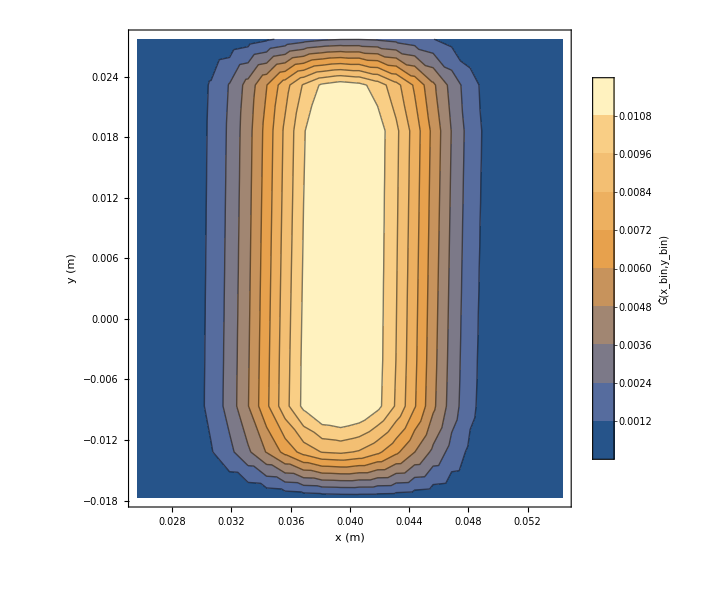

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1060/"];
```

```mathematica
drFSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drFSpectruma1060=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1060,1];
```

```mathematica
drFSpectruma1055[[All,2]]//Length
```

264

```mathematica
drFSpectruma1060[[All,2]]//Length
```

256

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1060[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,«11»,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,«214»},{«1»},{«1»}} cannot be transposed.

ListPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[{{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375},{-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225},{0.,4.47425×10^-7,6.02744×10^-7,5.91973×10^-7,5.81468×10^-7,5.71224×10^-7,5.61233×10^-7,5.51489×10^-7,5.41986×10^-7,5.32718×10^-7,4.75389×10^-8,0.,0.0000879969,0.000119268,0.000117147,0.000115078,0.000113059,0.000111091,0.00010917,0.000107297,0.00010543,0.0000104977,0.,0.000701745,0.000952878,0.00093608,0.000919691,0.000903701,0.000888099,0.000872877,0.000858025,0.000839179,0.0000834952,3.5836×10^-6,0.00239433,0.00325997,0.00320344,0.00314825,0.00309437,0.00304178,0.00299043,0.00294031,0.00284975,0.000327453,0.000037155,0.00559804,0.00767238,0.00754283,0.00741622,0.0072925,0.00717161,0.00705348,0.00693807,0.00664837,0.000848306,0.000165113,0.0105384,0.0145972,0.0143612,0.0141301,0.0139039,0.0136825,0.0134658,0.0132537,0.0125429,0.00178018,0.000466438,0.0171219,0.0240336,0.0236801,0.0233297,0.022985,0.0226459,0.0223126,0.021985,0.0205558,0.00321438,0.00096978,0.0246906,0.0351399,0.0347259,0.0342925,0.0338625,0.0334367,0.0330126,0.0325974,0.0301499,0.00514795,0.00159149,0.0322596,0.0464223,0.0460451,0.0455901,0.0451366,0.0446842,0.0442341,0.0437851,0.0401522,0.0544281,0.0540196,0.0492595,0.00942923,0.00266363,0.0428271,0.0626197,0.0626168,0.0623765,0.0621288,0.0618731,0.0616107,0.0613375,0.05573,0.011033,0.00295451,0.0436845,0.0643068,0.0645062,0.0644428,0.06436,0.0642704,0.064177,0.0640722,0.0580227,0.0118582,0.00307535,0.0419021,0.0620969,0.0624748,0.062525,0.0625699,0.0626116,0.062647,0.0626745,0.0564962,0.0119396,0.00302753,0.0378254,0.056474,0.0569931,0.0571759,0.0573524,0.0575234,0.057676,0.0578325,0.0519097,0.0113495,0.00278236,0.0317647,0.0478165,0.0484712,0.0487879,0.0490987,0.0494035,0.049702,0.0499907,0.0446863,0.010074,0.00232516,0.0244053,0.0370302,0.0377635,0.0381813,0.0385945,0.0390033,0.0394075,0.0398029,0.0354729,0.00833864,0.00171419,0.0167922,0.0256606,0.0263695,0.0268248,0.0272801,0.0277306,0.0281806,0.0286239,0.0254997,0.00619068,0.00108409,0.0098629,0.015269,0.015852,0.0162725,0.0166946,0.0171238,0.0175441,0.0179669,0.0160051,0.00404876,0.000562323,0.00473851,0.00745261,0.00782324,0.00811736,0.00841886,0.00872724,0.00904185,0.00936082,0.00832003,0.00225943,0.000226292,0.00197739,0.00313934,0.00331034,0.00345557,0.00360644,0.00376261,0.00392418,0.0040914,0.00361137,0.00103357,0.0000710994,0.000718059,0.00114017,0.00121167,0.00127949,0.00135001,0.00142319,0.00149911,0.00157783,0.00141378,0.000393956,0.0000121256,0.000189393,0.000301593,0.000326884,0.000353033,0.000380663,0.000409764,0.000440381,0.000472558,0.000439617,0.00011556,4.52877×10^-7,0.0000258848,0.0000418482,0.0000476277,0.0000539891,0.0000609723,0.000068562,0.0000768318,0.0000858192,0.0000850529,0.0000185858,0.,6.46386×10^-7,1.16186×10^-6,1.71743×10^-6,2.60735×10^-6,2.55523×10^-6,3.22825×10^-6,4.01108×10^-6,5.00119×10^-6,5.74377×10^-6,1.0528×10^-6}}],PlotRange→All]

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0250021,-0.0199964} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
dBRxBSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0250006,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

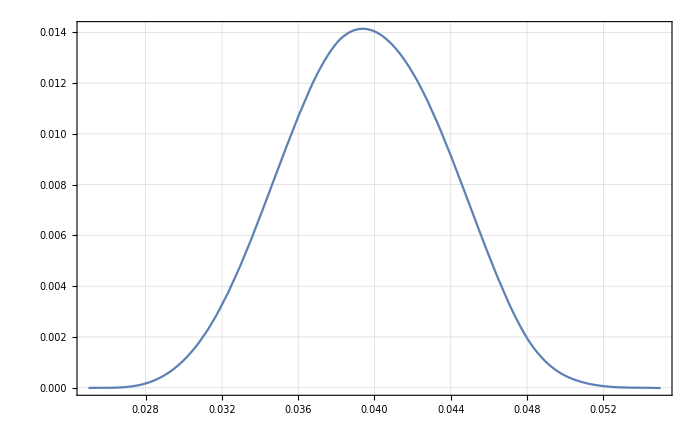

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0250006,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

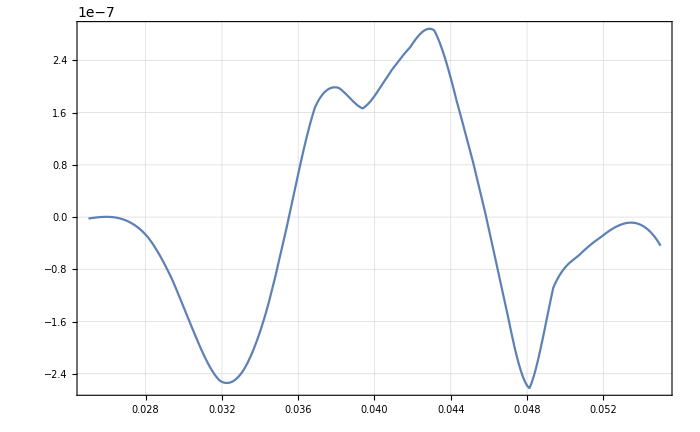

```mathematica
Plot[{RefSpectrumInter[x,0.]-dBRxBSpectruma1055Inter[x,0.]},{x,0.025,0.055},PlotRange->All]
```

```mathematica
dBRxBSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]]}]];
dBRxBSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1045[[All,2]]/Total[dAlphaSpectruma1045[[All,2]]]}]];
dBRxBSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1055[[All,2]]/Total[dAlphaSpectruma1055[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0250006,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

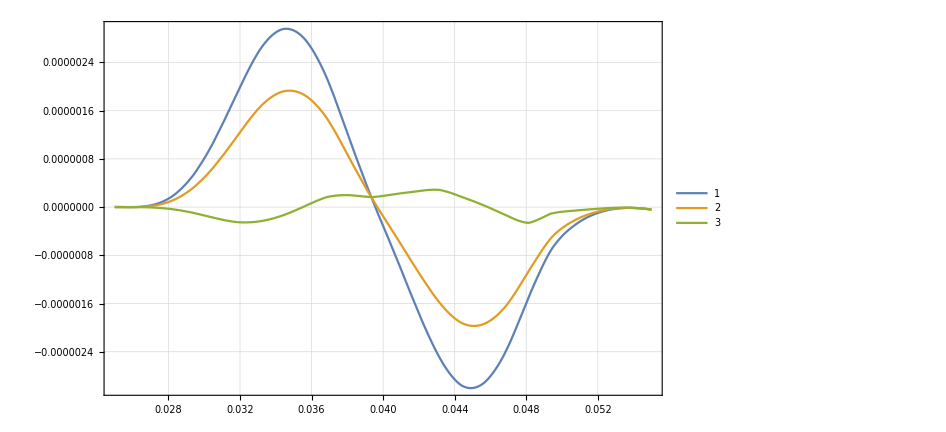

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBRxBSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectruma1055Inter[x,0.]

}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
ListPlot[Total[(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-#)^2]&/@BRxBDataList]
```

ListPlot::lpn: BRxBDataList is not a list of numbers or pairs of numbers.

ListPlot[BRxBDataList]

```mathematica
dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.36863×10^-10,4.07996×10^-10,3.19292×10^-11,1.42553×10^-13,0.,0.,0.,0.,0.,0.,2.59993×10^-9,1.4643×10^-7,3.11107×10^-7,2.31112×10^-7,1.36065×10^-7,4.76193×10^-8,1.2291×10^-9,0.,0.,0.,0.,2.03998×10^-7,3.11947×10^-6,6.84058×10^-6,6.62686×10^-6,4.83431×10^-6,1.93743×10^-6,1.46401×10^-7,0.,0.,0.,7.05888×10^-10,3.16048×10^-6,0.0000234196,0.0000493116,0.0000531614,0.0000408369,0.0000188314,2.86494×10^-6,9.03721×10^-9,0.,0.,3.23234×10^-7,0.0000177044,0.000100397,0.000205907,0.000234623,0.000186966,0.0000927304,0.0000185237,5.51569×10^-7,0.,0.,9.71469×10^-7,0.0000595062,0.000309378,0.000628561,0.000736105,0.000600097,0.000310256,0.0000712827,3.0292×10^-6,0.,0.,2.74528×10^-6,0.000152579,0.000774239,0.00159952,0.0018878,0.00156135,0.000823198,0.000199853,9.54737×10^-6,0.,0.,3.88467×10^-6,0.000313669,0.00168782,0.00369996,0.00433486,0.00363987,0.00190851,0.000449662,0.0000222802,0.,0.,0.,0.000531094,0.00323004,0.00773746,0.00898466,0.00770991,0.00398244,0.000844609,0.0000358352,0.,0.,0.,0.000740222,0.00535976,0.0139127,0.0161335,0.0141924,0.0072312,0.00135022,0.0000226273,0.,0.,0.,0.000863278,0.00775098,0.0214202,0.0249538,0.0223604,0.0112936,0.00185325,7.06033×10^-7,0.,0.,0.,0.000809817,0.00986941,0.0288684,0.0337018,0.0306964,0.0153352,0.00211014,0.,0.,0.,0.,0.00054451,0.0110646,0.0345881,0.0402363,0.0373612,0.0183953,0.00197547,0.,0.,0.,0.,0.000206637,0.0108394,0.0369185,0.0424076,0.0403525,0.0194847,0.00143803,0.,0.,0.,0.,0.0000203655,0.00914436,0.0348098,0.0391745,0.0382876,0.0180841,0.000732696,0.,0.,0.,0.,0.,0.00645827,0.0283774,0.0311792,0.0311918,0.014377,0.000241551,0.,0.,0.,0.,0.,0.00375251,0.019043,0.0204596,0.0208311,0.00937791,0.000013516,0.,0.,0.,0.,0.,0.00163446,0.00951662,0.0100221,0.0102987,0.00457549,0.,0.,0.,0.,0.,0.,0.000440399,0.00285973,0.00296835,0.00305719,0.00136139,0.,0.,0.,0.,0.,0.,0.0000450576,0.000308296,0.000317597,0.000327138,0.000146399,0.,0.,0.,0.,0.,0.,4.85721×10^-8,3.66074×10^-7,3.75038×10^-7,3.84282×10^-7,6.12352×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## manual chi^2 investigation

```mathematica
-0.104<-0.106
```

False

```mathematica
10
```

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
rFDataList={drFSpectruma1040[[All,2]]/Total[drFSpectruma1040[[All,2]]],drFSpectruma1045[[All,2]]/Total[drFSpectruma1045[[All,2]]],drFSpectruma0[[All,2]]/Total[drFSpectruma0[[All,2]]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055}
```

{-0.104,-0.1045,-0.105,-0.1055}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

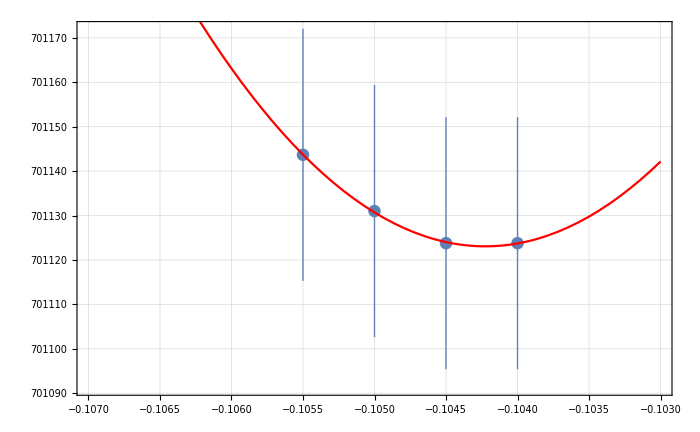
{{{0.000701124,0.000701124,0.000701131,0.000701144},{2.83675×10^-8,2.83675×10^-8,2.83678×10^-8,2.83683×10^-8}},a0 =  | -0.104226
FittedModel[0.000701123+0.012712 (0.104226+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104226 | 0.00254456 | -40.9602 | 0.0155393
scale | 0.012712 | 0.0567355 | 0.224058 | 0.859678
yoffset | 0.000701123 | 1.95643×10^-8 | 35836.8 | 0.0000177644 | 
 | DF | SS | MS
Model | 3 | 2.44347×10^9 | 8.14491×10^8
Error | 1 | 0.000200582 | 0.000200582
Uncorrected Total | 4 | 2.44347×10^9 | 
Corrected Total | 3 | 0.327996 |  | ,-Graphics-}

```mathematica
rFInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rFDataList,bList, 4]
```

```mathematica
(-0.104225548356761+0.105)/-0.105
```

-0.00737573

```mathematica
-0.105+(0.105*0.01)
```

-0.10395

```mathematica
-0.1042255483567612
```

```mathematica
rFInvest[[2,1,1,2]]
```

-0.104226

```mathematica
(rFInvest[[2,1,1,2]]+0.105)/-0.105/(10^-4)
```

-73.7573

```mathematica
73.75729935607534*10^-4
```

0.00737573

# dBRxB, k=-15.13

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b0/"];
```

```mathematica
dBRxBSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_1-96.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_97-112.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_113-128.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_129-144.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_145-160.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_161-176.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_177-192.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_193-253.txt}

```mathematica
dBRxBSpectrumb0=Flatten[Table[Import[dBRxBSubFileNamesb0[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b15/"];
```

```mathematica
dBRxBSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_1-96.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_97-112.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_113-128.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_129-144.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_145-160.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_161-176.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_177-192.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_193-253.txt}

```mathematica
dBRxBSpectrumb15=Flatten[Table[Import[dBRxBSubFileNamesb15[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b7/"];
```

```mathematica
dBRxBSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_1-96.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_97-112.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_113-128.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_129-144.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_145-160.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_161-176.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_177-192.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_193-253.txt}

```mathematica
dBRxBSpectrumb75=Flatten[Table[Import[dBRxBSubFileNamesb75[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b-7/"];
```

```mathematica
dBRxBSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_1-96.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_97-112.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_113-128.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_129-144.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_145-160.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_161-176.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_177-192.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_193-253.txt}

```mathematica
dBRxBSpectrumbm75=Flatten[Table[Import[dBRxBSubFileNamesbm75[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b-15/"];
```

```mathematica
dBRxBSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_1-96.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_97-112.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_113-128.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_129-144.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_145-160.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_161-176.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_177-192.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_193-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dBRxBSpectrumbm15=Flatten[Import[#,"Table"]&/@dBRxBSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,-0.05,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
dBRxBSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,-0.05,0.04},PlotRange->All]
```

-Graphics-

```mathematica
Plot[{RefSpectrumInter[x,0.],dBRxBSpectrumb0Inter[x,0.]},{x,-0.05,0.04},PlotRange->All]
```

-Graphics-

```mathematica
dBRxBSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]]}]];
dBRxBSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm75[[All,2]]/Total[dBRxBSpectrumbm75[[All,2]]]}]];
dBRxBSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb15[[All,2]]/Total[dBRxBSpectrumb15[[All,2]]]}]];
dBRxBSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}]];
```

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBRxBSpectrumbm15Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumbm75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb0Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb15Inter[x,0.]
}
,{x,-0.05,0.04},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Total[(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-#)^2]&/@BRxBDataList]
```

ListPlot::lpn: BRxBDataList is not a list of numbers or pairs of numbers.

ListPlot[BRxBDataList]

```mathematica
dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.36863×10^-10,4.07996×10^-10,3.19292×10^-11,1.42553×10^-13,0.,0.,0.,0.,0.,0.,2.59993×10^-9,1.4643×10^-7,3.11107×10^-7,2.31112×10^-7,1.36065×10^-7,4.76193×10^-8,1.2291×10^-9,0.,0.,0.,0.,2.03998×10^-7,3.11947×10^-6,6.84058×10^-6,6.62686×10^-6,4.83431×10^-6,1.93743×10^-6,1.46401×10^-7,0.,0.,0.,7.05888×10^-10,3.16048×10^-6,0.0000234196,0.0000493116,0.0000531614,0.0000408369,0.0000188314,2.86494×10^-6,9.03721×10^-9,0.,0.,3.23234×10^-7,0.0000177044,0.000100397,0.000205907,0.000234623,0.000186966,0.0000927304,0.0000185237,5.51569×10^-7,0.,0.,9.71469×10^-7,0.0000595062,0.000309378,0.000628561,0.000736105,0.000600097,0.000310256,0.0000712827,3.0292×10^-6,0.,0.,2.74528×10^-6,0.000152579,0.000774239,0.00159952,0.0018878,0.00156135,0.000823198,0.000199853,9.54737×10^-6,0.,0.,3.88467×10^-6,0.000313669,0.00168782,0.00369996,0.00433486,0.00363987,0.00190851,0.000449662,0.0000222802,0.,0.,0.,0.000531094,0.00323004,0.00773746,0.00898466,0.00770991,0.00398244,0.000844609,0.0000358352,0.,0.,0.,0.000740222,0.00535976,0.0139127,0.0161335,0.0141924,0.0072312,0.00135022,0.0000226273,0.,0.,0.,0.000863278,0.00775098,0.0214202,0.0249538,0.0223604,0.0112936,0.00185325,7.06033×10^-7,0.,0.,0.,0.000809817,0.00986941,0.0288684,0.0337018,0.0306964,0.0153352,0.00211014,0.,0.,0.,0.,0.00054451,0.0110646,0.0345881,0.0402363,0.0373612,0.0183953,0.00197547,0.,0.,0.,0.,0.000206637,0.0108394,0.0369185,0.0424076,0.0403525,0.0194847,0.00143803,0.,0.,0.,0.,0.0000203655,0.00914436,0.0348098,0.0391745,0.0382876,0.0180841,0.000732696,0.,0.,0.,0.,0.,0.00645827,0.0283774,0.0311792,0.0311918,0.014377,0.000241551,0.,0.,0.,0.,0.,0.00375251,0.019043,0.0204596,0.0208311,0.00937791,0.000013516,0.,0.,0.,0.,0.,0.00163446,0.00951662,0.0100221,0.0102987,0.00457549,0.,0.,0.,0.,0.,0.,0.000440399,0.00285973,0.00296835,0.00305719,0.00136139,0.,0.,0.,0.,0.,0.,0.0000450576,0.000308296,0.000317597,0.000327138,0.000146399,0.,0.,0.,0.,0.,0.,4.85721×10^-8,3.66074×10^-7,3.75038×10^-7,3.84282×10^-7,6.12352×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
BRxBDataList={dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]],dBRxBSpectrumbm75[[All,2]]/Total[dBRxBSpectrumbm75[[All,2]]],dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]],dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]],dBRxBSpectrumb15[[All,2]]/Total[dBRxBSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

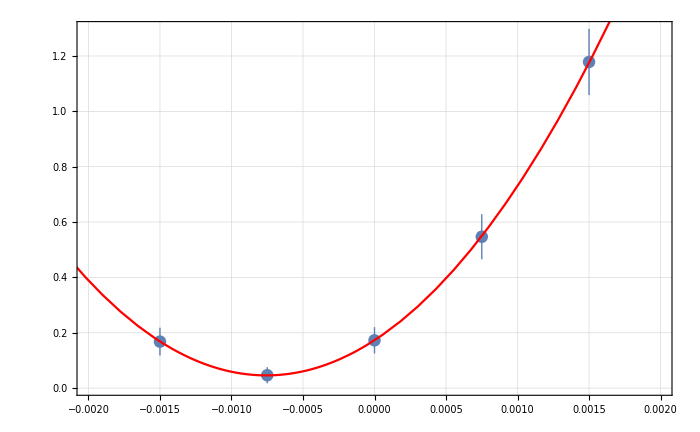
{{{1.67947×10^-10,4.64371×10^-11,1.7259×10^-10,5.46827×10^-10,1.17847×10^-9},{5.02571×10^-11,2.93313×10^-11,4.7551×10^-11,8.1608×10^-11,1.19841×10^-10}},b0 =  | -0.000756452
FittedModel[4.59438×10^-11+0.000221834 (0.000756452+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000756452 | 0.0000982889 | -7.6962 | 0.016467
scale | 0.000221834 | 0.0000303947 | 7.29843 | 0.0182607
yoffset | 4.59438×10^-11 | 2.41516×10^-11 | 1.90231 | 0.197472 | 
 | DF | SS | MS
Model | 3 | 168.444 | 56.1481
Error | 2 | 0.00208928 | 0.00104464
Uncorrected Total | 5 | 168.447 | 
Corrected Total | 4 | 109.764 |  | ,-Graphics-}

```mathematica
BRxBInvest=TransferToRefParableFit[RefSpectrum[[All,2]],BRxBDataList,bList, 4]
```

```mathematica
BRxBInvest[[2,1,1,2]]/(5*10^-5)
```

-15.129